```mathematica
SetDirectory[NotebookDirectory[]];
(*FHN Parameters*)
ep=0.08;β=0.65;γ=0.7;
(*Look for stable equilibrium*)
eqn=FindRoot[0==v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
```

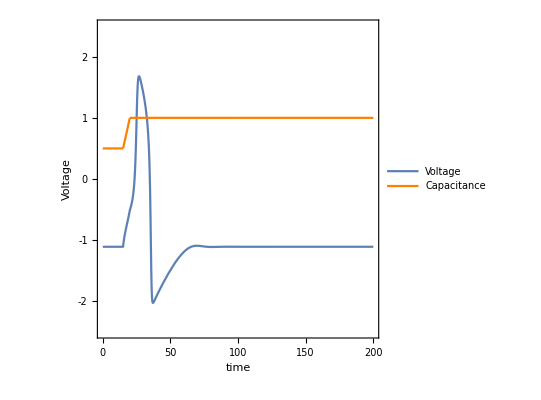

Fig4a.png

```mathematica
(*Figure A*)
(*Capacitance function*)
T=100;C0=0.5;C1=1;τ1=0.15;τ2=0.2;τ3=0.9;maxtime=200;
Ct[t_]=Which[
t<τ1 T,C0,
t<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), 
t<τ3 T,C1, 
True,C1
];
Ctd[t_]=Which[
t<τ1 T,0,
t<τ2 T,(C1-C0)/(τ2 T- τ1 T), 
t<τ3 T,0, 
True,0
];
(*Simulation*)
{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
FrameTicks->{{All,All},{All,None}}
];
(*,ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],
ColorFunctionScaling->False,PlotLegends->Placed[StringJoin["C0=",ToString[C0],", C1=",ToString[C1],", T= ",ToString[T],",\n","τ1= ",ToString[τ1],", τ2= ",ToString[τ2],", τ3= ",ToString[τ3],",\n","ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]];*)
capacitance=Plot[Ct[t],{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];
g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]}],{{0.7,0.9}}]]
Export["Fig4a.png",g1]
```

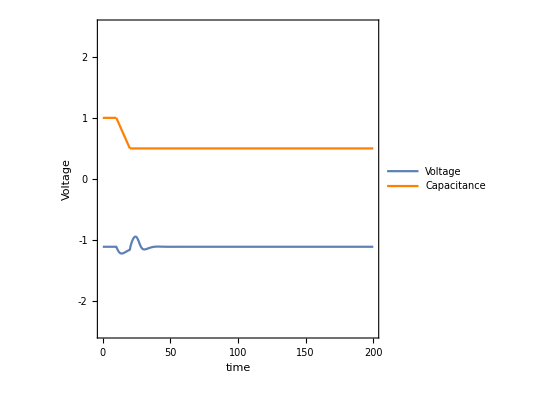

Fig4b.png

```mathematica
(*Figure B*)
(*Capacitance function*)
T=100;C0=1;C1=0.5;τ1=0.1;τ2=0.2;τ3=0.9;maxtime=200;
Ct[t_]=Which[
t<τ1 T,C0,
t<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), 
t<τ3 T,C1, 
True,C1
];
Ctd[t_]=Which[
t<τ1 T,0,
t<τ2 T,(C1-C0)/(τ2 T- τ1 T), 
t<τ3 T,0, 
True,0
];

{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
FrameTicks->{{All,All},{All,None}}
];
capacitance=Plot[Ct[t],{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];
g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]}],{{0.7,0.9}}]]
Export["Fig4b.png",g1]
```

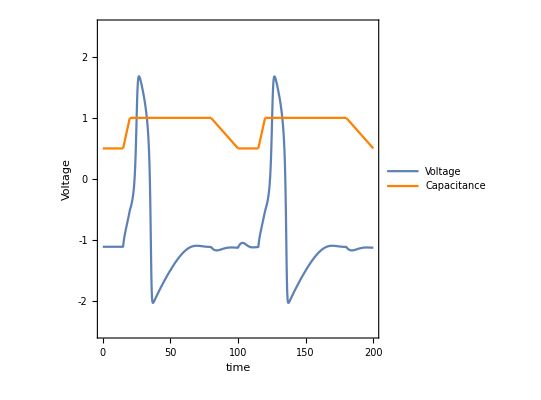

Fig4c.png

```mathematica
(*Figure C*)
T=100;C0=0.5;C1=1;τ1=0.15;τ2=0.2;τ3=0.8;maxtime=200;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];

{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
FrameTicks->{{All,All},{All,None}}
];
capacitance=Plot[Ct[t],{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];
g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]}],{{0.7,0.9}}]]
Export["Fig4c.png",g1]
```

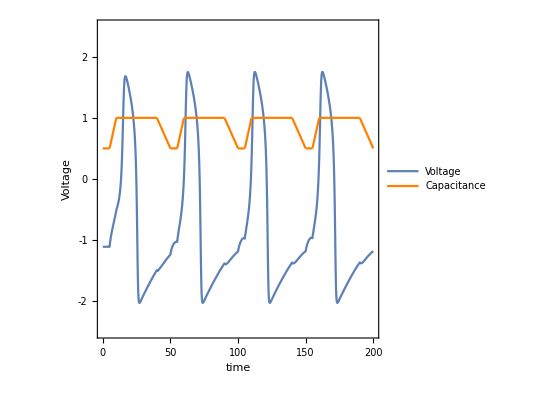

Fig4d.png

```mathematica
(*Figure D*)
maxtime=200;
T=50;C0=0.5;C1=1;τ1=0.1;τ2=0.2;τ3=0.8;
Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(Mod[t,T]-τ1 T)(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T]-τ3 T)(C0-C1)/(T- τ3 T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/(τ2 T- τ1 T), Mod[t,T]<τ3 T,0, True,(C0-C1)/(T- τ3 T)];

{V,W}=NDSolveValue[{Ct[t] v'[t]+v[t] Ctd[t] ==v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==v0,w[0]==w0},{v,w},{t,0,maxtime},MaxStepSize->0.01Min[τ2-τ1,1-τ3]T];
(*Voltage/capacitance plot*)
voltage=Plot[V[t],{t,0,maxtime},
PlotRange->{-2.5,2.5},
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
FrameTicks->{{All,All},{All,None}}
];
capacitance=Plot[Ct[t],{t,0,maxtime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];
g1=Legended[Show[voltage, capacitance,AspectRatio->1],Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},{Style["Voltage",FontSize->18],Style["Capacitance",FontSize->18]}],{{0.7,0.9}}]]
Export["Fig4d.png",g1]
```